## For small angular momentum:

200

10

0.1

0.7

π/2

0.525

59.1

0.6

1

-1050. Cos[θ[t]]+29.55 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+0.3 (Cos[θ[t]] ϕ'[t]+ψ'[t])^2

{0.6 (-Sin[θ[t]] θ'[t] ϕ'[t]+Cos[θ[t]] ϕ''[t]+ψ''[t])==0,-1050. Sin[θ[t]]-59.1 Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+0.6 Sin[θ[t]] ϕ'[t] (Cos[θ[t]] ϕ'[t]+ψ'[t])+59.1 θ''[t]==0,118.2 Cos[θ[t]] Sin[θ[t]] θ'[t] ϕ'[t]-0.6 Sin[θ[t]] θ'[t] (Cos[θ[t]] ϕ'[t]+ψ'[t])+59.1 Sin[θ[t]]^2 ϕ''[t]+0.6 Cos[θ[t]] (-Sin[θ[t]] θ'[t] ϕ'[t]+Cos[θ[t]] ϕ''[t]+ψ''[t])==0}

{θ[0]==π/2,ϕ[0]==0,ψ[0]==0,θ'[0]==0,ϕ'[0]==0,ψ'[0]==1}

{{θ→InterpolatingFunction[…],ψ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

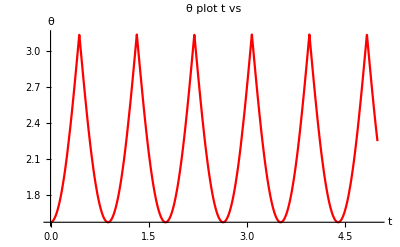

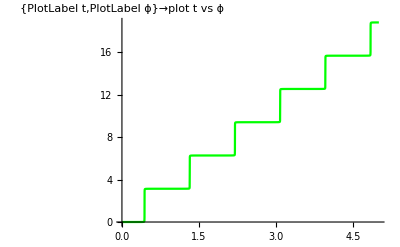

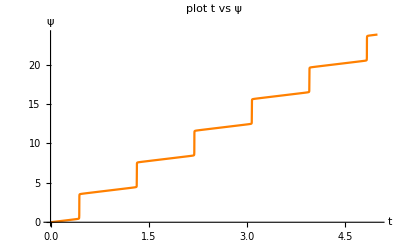

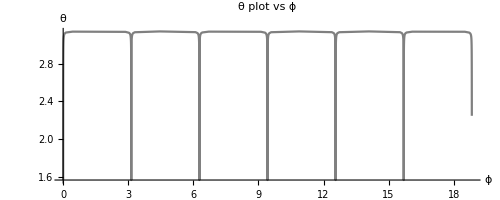

```mathematica
m=200
g=10
r=.1
h=.7
θ0=π/2
cm=3 h/4
I1=m(3 h^2/5+3 r^2/20)
I3=3m r^2/10
ω30=1

L=1/2*I3*(ψ'[t]+ϕ'[t]*Cos[θ[t]])^2+1/2*I1*((ϕ'[t])^2*(Sin[θ[t]])^2+(θ'[t])^2)-m*g*cm*Cos[θ[t]]
eqs={D[(D[L,ψ'[t]]), t]-D[L,ψ[t]]==0,
D[(D[L,θ'[t]]), t]-D[L,θ[t]]==0,
D[(D[L,ϕ'[t]]), t]-D[L,ϕ[t]]==0}

conditions={θ[0]==θ0,ϕ[0]==0,ψ[0]==0,θ'[0]==0,ϕ'[0]==0,ψ'[0]==ω30}

sol=NDSolve[{eqs,conditions},{θ,ψ,ϕ},{t,0,20}]
Plot[Evaluate[θ[t]/.sol],{t,0,5},AxesLabel->{HoldForm[t],HoldForm[θ]},PlotLabel->θ vs t plot,PlotStyle->Red]
Plot[Evaluate[ϕ[t]/.sol],{t,0,5},AxesLabel->{HoldForm[t],HoldForm[ϕ]}PlotLabel->ϕ vs t plot,PlotStyle->Green]
Plot[Evaluate[ψ[t]/.sol],{t,0,5},AxesLabel->{HoldForm[t],HoldForm[ψ]},PlotLabel->ψ vs t plot,PlotStyle->Orange]
ParametricPlot[Evaluate[{ϕ[t],θ[t]}/.sol],{t,0,5},AxesLabel->{HoldForm[ϕ],HoldForm[θ]},PlotLabel->θ vs ϕ plot,PlotStyle->Gray]
```

## For large angular momentum (note that the periode has decreased sooooo much):

200

10

0.1

0.7

π/2

0.525

59.1

0.6

50000

50000

-1050. Cos[θ[t]]+29.55 (θ'[t]^2+Sin[θ[t]]^2 ϕ'[t]^2)+0.3 (Cos[θ[t]] ϕ'[t]+ψ'[t])^2

{0.6 (-Sin[θ[t]] θ'[t] ϕ'[t]+Cos[θ[t]] ϕ''[t]+ψ''[t])==0,-1050. Sin[θ[t]]-59.1 Cos[θ[t]] Sin[θ[t]] ϕ'[t]^2+0.6 Sin[θ[t]] ϕ'[t] (Cos[θ[t]] ϕ'[t]+ψ'[t])+59.1 θ''[t]==0,118.2 Cos[θ[t]] Sin[θ[t]] θ'[t] ϕ'[t]-0.6 Sin[θ[t]] θ'[t] (Cos[θ[t]] ϕ'[t]+ψ'[t])+59.1 Sin[θ[t]]^2 ϕ''[t]+0.6 Cos[θ[t]] (-Sin[θ[t]] θ'[t] ϕ'[t]+Cos[θ[t]] ϕ''[t]+ψ''[t])==0}

{θ[0]==π/2,ϕ[0]==0,ψ[0]==0,θ'[0]==0,ϕ'[0]==0,ψ'[0]==50000}

{{θ→InterpolatingFunction[…],ψ→InterpolatingFunction[…],ϕ→InterpolatingFunction[…]}}

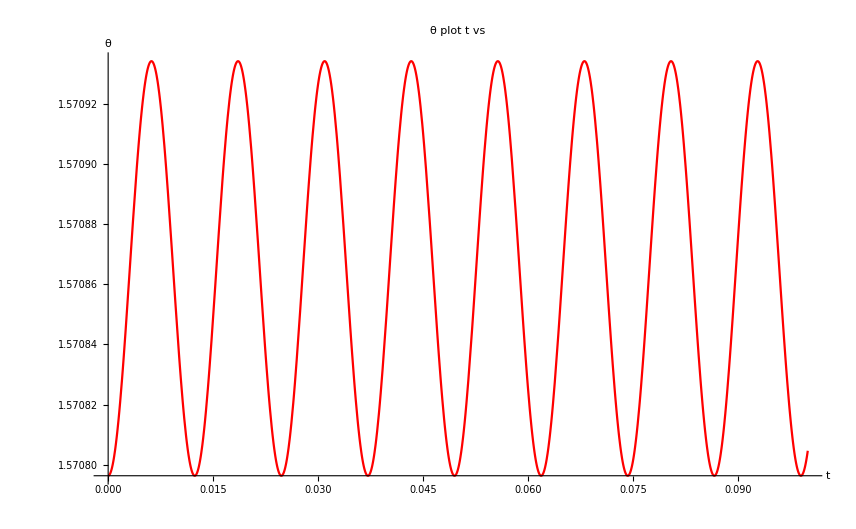

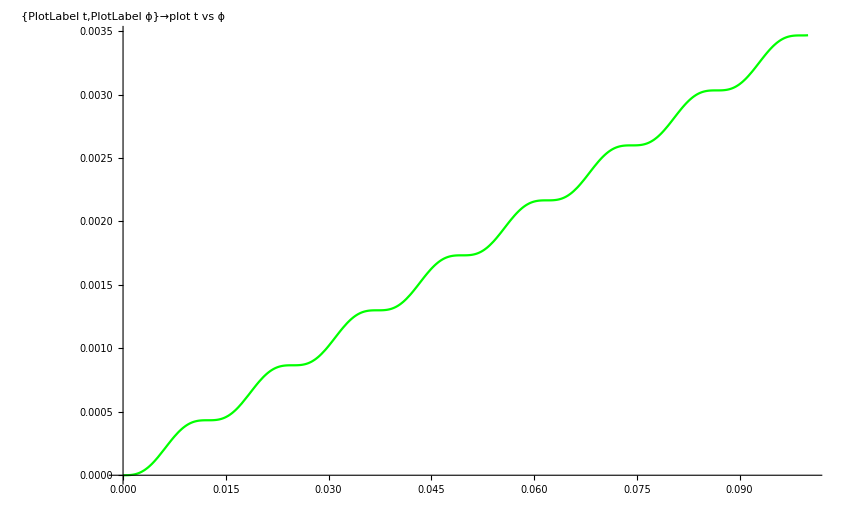

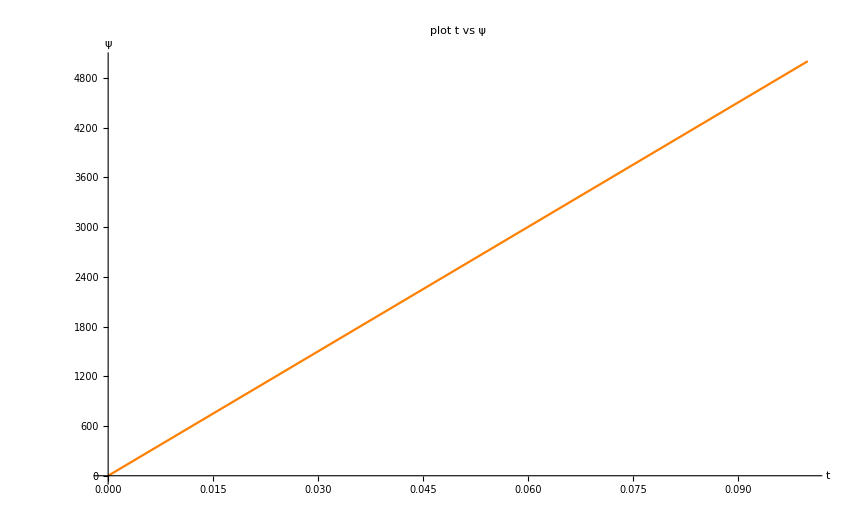

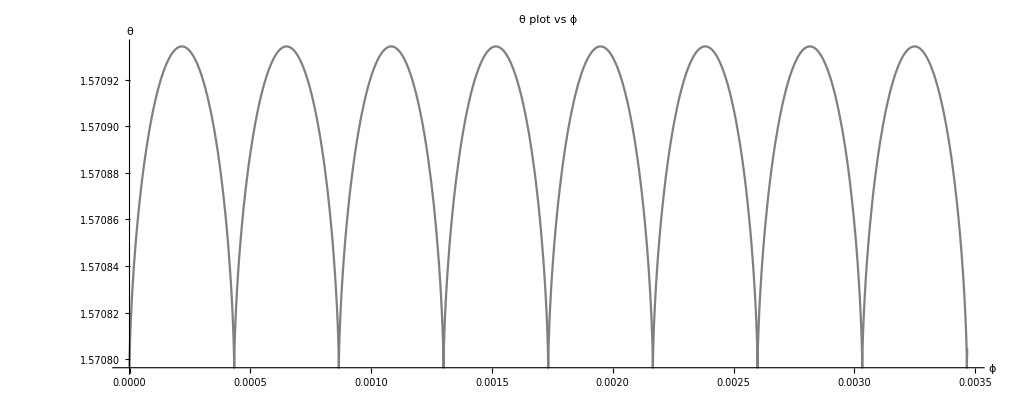

```mathematica
m=200
g=10
r=.1
h=.7
θ0=π/2
cm=3 h/4
I1=m(3 h^2/5+3 r^2/20)
I3=3m r^2/10
k=50000
ω30=k

L=1/2*I3*(ψ'[t]+ϕ'[t]*Cos[θ[t]])^2+1/2*I1*((ϕ'[t])^2*(Sin[θ[t]])^2+(θ'[t])^2)-m*g*cm*Cos[θ[t]]
eqs={D[(D[L,ψ'[t]]), t]-D[L,ψ[t]]==0,
D[(D[L,θ'[t]]), t]-D[L,θ[t]]==0,
D[(D[L,ϕ'[t]]), t]-D[L,ϕ[t]]==0}

conditions={θ[0]==θ0,ϕ[0]==0,ψ[0]==0,θ'[0]==0,ϕ'[0]==0,ψ'[0]==ω30}

sol=NDSolve[{eqs,conditions},{θ,ψ,ϕ},{t,0,2}]
Plot[Evaluate[θ[t]/.sol],{t,0,0.1},AxesLabel->{HoldForm[t],HoldForm[θ]},PlotLabel->θ vs t plot,PlotStyle->Red]
Plot[Evaluate[ϕ[t]/.sol],{t,0,0.1},AxesLabel->{HoldForm[t],HoldForm[ϕ]}PlotLabel->ϕ vs t plot,PlotStyle->Green]
Plot[Evaluate[ψ[t]/.sol],{t,0,0.1},AxesLabel->{HoldForm[t],HoldForm[ψ]},PlotLabel->ψ vs t plot,PlotStyle->Orange]
ParametricPlot[Evaluate[{ϕ[t],θ[t]}/.sol],{t,0,0.1},AxesLabel->{HoldForm[ϕ],HoldForm[θ]},PlotLabel->θ vs ϕ plot,PlotStyle->Gray]
```